```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

## Parameters

```mathematica
(*Approximations: complexes are in equilibrium, effectors are conserved.

 r+k <-->C

c+e ->a+e
*)
```

```mathematica
gR=1; (*NLR growth*)
gK1=10;
gK2=10;
gK3=10;
gK4=0;
gK5=0;
gK6=0;
gK={gK1,gK2,gK3,gK4,gK5,gK6};
deltaR=1; (*NLR decay*)
deltaK=1; (*kinase decay*)
deltaC=1; (*complex decay*)
(*effector-target unbinding*)
```

```mathematica
alphaF=0.5; (*R-T complex formation*)
alphaB=1; (*R-T complex unbinding*)
gamma1=0.5;  (*complex-effector binding*)
gamma2=5; (*complex-effector unbinding*)
```

```mathematica
e0=3; (*total effector concentration*)
```

## Equations

```mathematica
(*solve for E based on e0 and quasi-equilibrium*)
```

```mathematica
fixedEEq=x+(beta1/beta2)*tVar*x+(gamma1/gamma2)*rVar*tVar*x*alphaF/(alphaB+gamma1*x)-e0Var==0;
fixedSol=x/.Solve[fixedEEq,x];
(*getE[thisR_?NumericQ,thisT_?NumericQ,thisE0_?NumericQ]:=Module[{numericSol,final},

numericSol=fixedSol/.{rVar->thisR,tVar->thisT,e0Var->thisE0}//N;
Sort[numericSol];
If[(numericSol[[1]]<0)&&(numericSol[[2]]>0),final=numericSol[[2]],final="error"];
final
]*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*simple approximation: Subscript[γ, 2]>>Subscript[γ, 1], so e_i-->Ei*)
```

```mathematica
(*Z=alpha_F*sum_i k_i*gamma1*ei/(alphaB+gamma1*ei)*)
```

```mathematica
(*r sink includes decay*)
getZR[kVec_,eVec_]:=Module[{thisZ},
(* return Z*)
thisTable=Table[kVec[[i]]*(gamma1*eVec[[i]]+deltaC)/(alphaB+gamma1*eVec[[i]]+deltaC),{i,Length[eVec]}];
thisZ=alphaF*Total[thisTable];
thisZ
]
```

```mathematica
(*activation does not include complex decay*)

getZA[kVec_,eVec_]:=Module[{thisZ},
(* return Z*)
thisTable=Table[kVec[[i]]*(gamma1*eVec[[i]])/(alphaB+gamma1*eVec[[i]]+deltaC),{i,Length[eVec]}];
thisZ=alphaF*Total[thisTable];
thisZ
]
```

```mathematica
drds[rVar_,aVar_,kVec_,eVec_]:=Module[{thisZ},

(*thisE=getE[rVar,tVar,e0Var];*)
thisZ=getZR[kVec,eVec];
gR-deltaR*rVar-rVar*thisZ+f[aVar]
]
```

```mathematica
dads[rVar_,aVar_,kVec_,eVec_]:=Module[{thisZ},

(*thisE=getE[rVar,tVar,e0Var];*)

thisZ=getZA[kVec,eVec];
rVar*thisZ-deltaR*aVar
]
(*dads=r[s]*t[s]*e*z;*)
```

```mathematica
(*we'll define separate k variables, but use one deriv fn*)
dkids[rVar_,aVar_,kVec_,eVec_,kIndex_]:=Module[{thisZ},

(*thisE=getE[rVar,tVar,e0Var];*)
gK[[kIndex]]-deltaK*kVec[[kIndex]]-alphaF*rVar*kVec[[kIndex]]*(gamma1*eVec[[kIndex]]+deltaC)/(alphaB+gamma1*eVec[[kIndex]]+deltaC)+fk[aVar]
]
```

```mathematica
f[z_]:=z^2;(*feedback*)
```

```mathematica
fk[z_]:=0;(* kinase feedback*)
```

## solver

```mathematica
(* remove duplicates *)
processRoots[rootList_]:=Module[{cleanList,test,unique,thisDist,i,j},
cleanList={rootList[[1]]};
For[i=2,i<=Length[rootList],i++,

test=rootList[[i]];
unique=True;
For[j=1,j<=Length[cleanList],j++,
	thisDist=EuclideanDistance[test,cleanList[[j]]];
	If[thisDist<10^-5,unique=False];
];
If[unique==True,AppendTo[cleanList,test];];

];

cleanList
]
```

```mathematica
getFixedPoint[e0Var_]:=Module[{rootList,thisSol,thisGuess,guessList,cleanList,i,j,k},

guessList={0.1,1,10,100};
rootList={};
Print[e0Var];
For[i=1,i<=Length[guessList],i++,
For[j=1,j<=Length[guessList],j++,
For[k=1,k<=Length[guessList],k++,

thisSol=FindRoot[{drds[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var]==0,dads[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var]==0,dkids[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var,1]==0,dkids[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var,2]==0,dkids[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var,3]==0,dkids[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var,4]==0,dkids[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var,5]==0,dkids[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var,6]==0},{rVar,guessList[[i]],0,10^6},{k1Var,guessList[[j]],0,10^6},{k2Var,guessList[[j]],0,10^6},{k3Var,guessList[[j]],0,10^6},{k4Var,guessList[[j]],0,10^6},{k5Var,guessList[[j]],0,10^6},{k6Var,guessList[[j]],0,10^6},{aVar,guessList[[k]],0,10^6}];
residual=(drds[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var])^2+(dads[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var])^2/.thisSol; (*check convergence*)
If[residual<=10^-6,AppendTo[rootList,{rVar,aVar,k1Var,k2Var,k3Var,k4Var,k5Var,k6Var}/.thisSol];];
];
];
];
cleanList=processRoots[rootList];
cleanList
]
```

```mathematica
(*equal effector spread*)
```

```mathematica
(*fixedPointList=Table[{{i/6,i/6,i/6,i/6,i/6,i/6},getFixedPoint[{i/6,i/6,i/6,i/6,i/6,i/6}]},{i,0,20,0.1}];*)
```

```mathematica
(*unbalanced effectors*)
```

```mathematica
(*maxE=0.5;
otherE=(1-maxE)/5;*)
```

```mathematica
(*fixedPointList=Table[{{maxE*i,otherE*i,otherE*i,otherE*i,otherE*i,otherE*i},getFixedPoint[{maxE*i,otherE*i,otherE*i,otherE*i,otherE*i,otherE*i}]},{i,0,20,0.1}];*)
```

```mathematica
(*only e1*)
```

```mathematica
fixedPointList=Table[{{i,0,0,0,0,0},getFixedPoint[{i,0,0,0,0,0}]},{i,0,200,1}];
```

{0,0,0,0,0,0}

FindRoot::reged: The point {0.,0.113527,0.113527,0.113527,0.102324,0.102324,0.102324,9.98852} is at the edge of the search region {0.,1.×10^6} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.,0.10255,0.10255,0.10255,0.102438,0.102438,0.102438,99.9989} is at the edge of the search region {0.,1.×10^6} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {-1.38778×10^-17,1.046,1.046,1.046,1.02192,1.02192,1.02192,9.97532} is at the edge of the search region {0.,1.×10^6} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1,0,0,0,0,0}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

{2,0,0,0,0,0}

{3,0,0,0,0,0}

{4,0,0,0,0,0}

{5,0,0,0,0,0}

{6,0,0,0,0,0}

{7,0,0,0,0,0}

{8,0,0,0,0,0}

{9,0,0,0,0,0}

{10,0,0,0,0,0}

{11,0,0,0,0,0}

{12,0,0,0,0,0}

{13,0,0,0,0,0}

{14,0,0,0,0,0}

{15,0,0,0,0,0}

{16,0,0,0,0,0}

{17,0,0,0,0,0}

{18,0,0,0,0,0}

{19,0,0,0,0,0}

{20,0,0,0,0,0}

{21,0,0,0,0,0}

{22,0,0,0,0,0}

{23,0,0,0,0,0}

{24,0,0,0,0,0}

{25,0,0,0,0,0}

{26,0,0,0,0,0}

{27,0,0,0,0,0}

{28,0,0,0,0,0}

{29,0,0,0,0,0}

{30,0,0,0,0,0}

{31,0,0,0,0,0}

{32,0,0,0,0,0}

{33,0,0,0,0,0}

{34,0,0,0,0,0}

{35,0,0,0,0,0}

{36,0,0,0,0,0}

{37,0,0,0,0,0}

{38,0,0,0,0,0}

{39,0,0,0,0,0}

{40,0,0,0,0,0}

{41,0,0,0,0,0}

{42,0,0,0,0,0}

{43,0,0,0,0,0}

{44,0,0,0,0,0}

{45,0,0,0,0,0}

{46,0,0,0,0,0}

{47,0,0,0,0,0}

{48,0,0,0,0,0}

{49,0,0,0,0,0}

{50,0,0,0,0,0}

{51,0,0,0,0,0}

{52,0,0,0,0,0}

{53,0,0,0,0,0}

{54,0,0,0,0,0}

{55,0,0,0,0,0}

{56,0,0,0,0,0}

{57,0,0,0,0,0}

{58,0,0,0,0,0}

{59,0,0,0,0,0}

{60,0,0,0,0,0}

{61,0,0,0,0,0}

{62,0,0,0,0,0}

{63,0,0,0,0,0}

{64,0,0,0,0,0}

{65,0,0,0,0,0}

{66,0,0,0,0,0}

{67,0,0,0,0,0}

{68,0,0,0,0,0}

{69,0,0,0,0,0}

{70,0,0,0,0,0}

{71,0,0,0,0,0}

{72,0,0,0,0,0}

{73,0,0,0,0,0}

{74,0,0,0,0,0}

{75,0,0,0,0,0}

{76,0,0,0,0,0}

{77,0,0,0,0,0}

{78,0,0,0,0,0}

{79,0,0,0,0,0}

{80,0,0,0,0,0}

{81,0,0,0,0,0}

{82,0,0,0,0,0}

{83,0,0,0,0,0}

{84,0,0,0,0,0}

{85,0,0,0,0,0}

{86,0,0,0,0,0}

{87,0,0,0,0,0}

{88,0,0,0,0,0}

{89,0,0,0,0,0}

{90,0,0,0,0,0}

{91,0,0,0,0,0}

{92,0,0,0,0,0}

{93,0,0,0,0,0}

{94,0,0,0,0,0}

{95,0,0,0,0,0}

{96,0,0,0,0,0}

{97,0,0,0,0,0}

{98,0,0,0,0,0}

{99,0,0,0,0,0}

{100,0,0,0,0,0}

{101,0,0,0,0,0}

{102,0,0,0,0,0}

{103,0,0,0,0,0}

{104,0,0,0,0,0}

{105,0,0,0,0,0}

{106,0,0,0,0,0}

{107,0,0,0,0,0}

{108,0,0,0,0,0}

{109,0,0,0,0,0}

{110,0,0,0,0,0}

{111,0,0,0,0,0}

{112,0,0,0,0,0}

{113,0,0,0,0,0}

{114,0,0,0,0,0}

{115,0,0,0,0,0}

{116,0,0,0,0,0}

{117,0,0,0,0,0}

{118,0,0,0,0,0}

{119,0,0,0,0,0}

{120,0,0,0,0,0}

{121,0,0,0,0,0}

{122,0,0,0,0,0}

{123,0,0,0,0,0}

{124,0,0,0,0,0}

{125,0,0,0,0,0}

{126,0,0,0,0,0}

{127,0,0,0,0,0}

{128,0,0,0,0,0}

{129,0,0,0,0,0}

{130,0,0,0,0,0}

{131,0,0,0,0,0}

{132,0,0,0,0,0}

{133,0,0,0,0,0}

{134,0,0,0,0,0}

{135,0,0,0,0,0}

{136,0,0,0,0,0}

{137,0,0,0,0,0}

{138,0,0,0,0,0}

{139,0,0,0,0,0}

{140,0,0,0,0,0}

{141,0,0,0,0,0}

{142,0,0,0,0,0}

{143,0,0,0,0,0}

{144,0,0,0,0,0}

{145,0,0,0,0,0}

{146,0,0,0,0,0}

{147,0,0,0,0,0}

{148,0,0,0,0,0}

{149,0,0,0,0,0}

{150,0,0,0,0,0}

{151,0,0,0,0,0}

{152,0,0,0,0,0}

{153,0,0,0,0,0}

{154,0,0,0,0,0}

{155,0,0,0,0,0}

{156,0,0,0,0,0}

{157,0,0,0,0,0}

{158,0,0,0,0,0}

{159,0,0,0,0,0}

{160,0,0,0,0,0}

{161,0,0,0,0,0}

{162,0,0,0,0,0}

{163,0,0,0,0,0}

{164,0,0,0,0,0}

{165,0,0,0,0,0}

{166,0,0,0,0,0}

{167,0,0,0,0,0}

{168,0,0,0,0,0}

{169,0,0,0,0,0}

{170,0,0,0,0,0}

{171,0,0,0,0,0}

{172,0,0,0,0,0}

{173,0,0,0,0,0}

{174,0,0,0,0,0}

{175,0,0,0,0,0}

{176,0,0,0,0,0}

{177,0,0,0,0,0}

{178,0,0,0,0,0}

{179,0,0,0,0,0}

{180,0,0,0,0,0}

{181,0,0,0,0,0}

{182,0,0,0,0,0}

{183,0,0,0,0,0}

{184,0,0,0,0,0}

{185,0,0,0,0,0}

{186,0,0,0,0,0}

{187,0,0,0,0,0}

{188,0,0,0,0,0}

{189,0,0,0,0,0}

{190,0,0,0,0,0}

{191,0,0,0,0,0}

{192,0,0,0,0,0}

{193,0,0,0,0,0}

{194,0,0,0,0,0}

{195,0,0,0,0,0}

{196,0,0,0,0,0}

{197,0,0,0,0,0}

{198,0,0,0,0,0}

{199,0,0,0,0,0}

{200,0,0,0,0,0}

```mathematica
(*(e,list of fixed points)*)
(*fixedPointList=Table[{{i,1,0,0,0,0},getFixedPoint[{i,1,0,0,0,0}]},{i,0,20,0.1}];*)
```

```mathematica
(*convert a list where each e has a 3D ss, to coordinates for plotting. want r*(e), t*(e), a*(e)*)
getPlottingCoords[fixedPoints_]:=Module[{rPoints,aPoints,k1Points,k2Points,k3Points,k4Points,k5Points,k6Points},

rPoints={};
aPoints={};
k1Points={};
k2Points={};
k3Points={};
k4Points={};
k5Points={};
k6Points={};

For[i=1,i<=Length[fixedPoints],i++,

thisPoint=fixedPoints[[i]];
eValue=thisPoint[[1,1]]; (*just use Subscript[E, 1] for now*)

For[j=1,j<=Length[thisPoint[[2]]],j++,

thisFixedPoint=thisPoint[[2,j]];
AppendTo[rPoints,{eValue,thisFixedPoint[[1]]}];
AppendTo[aPoints,{eValue,thisFixedPoint[[2]]}];
AppendTo[k1Points,{eValue,thisFixedPoint[[3]]}];
AppendTo[k2Points,{eValue,thisFixedPoint[[4]]}];
AppendTo[k3Points,{eValue,thisFixedPoint[[5]]}];
AppendTo[k4Points,{eValue,thisFixedPoint[[6]]}];
AppendTo[k5Points,{eValue,thisFixedPoint[[7]]}];
AppendTo[k6Points,{eValue,thisFixedPoint[[8]]}];
];
];

{rPoints,aPoints,k1Points,k2Points,k3Points,k4Points,k5Points,k6Points}

]
```

```mathematica
{rCoords,aCoords,k1Coords,k2Coords,k3Coords,k4Coords,k5Coords,k6Coords}=getPlottingCoords[fixedPointList];
```

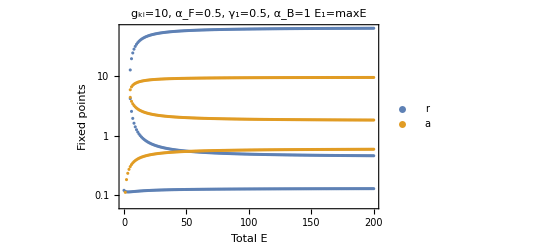

```mathematica
ListLogPlot[{rCoords,aCoords},PlotRange->{Automatic,Automatic},PlotLabel->"g_ki="<>ToString[gK1]<>", α_F="<>ToString[alphaF]<>", γ_1="<>ToString[gamma1]<>", α_B="<>ToString[alphaB]<>"\nE_1="<>ToString[maxE],PlotLegends->{"r","a"},FrameLabel->{"Total E","Fixed points"},LabelStyle->Directive[Black, 15],Frame->{True,True,False,False}]
```

```mathematica
(*Export["zar1_cDecay_gk1_"<>ToString[gK1]<>"_gk2_"<>ToString[gK2]<>"_ra.mx",{rCoords,aCoords}]*)
```

```mathematica
(*Export["cdecay_unequal.png",%]*)
```

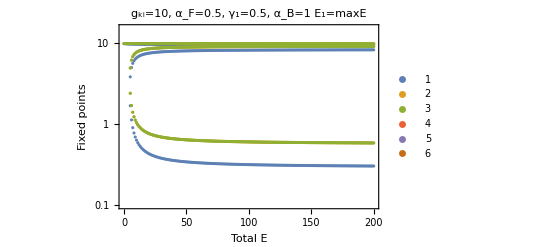

```mathematica
ListLogPlot[{k1Coords,k2Coords,k3Coords,k4Coords,k5Coords,k6Coords},PlotRange->{Automatic,{.1,15}},PlotLabel->"g_ki="<>ToString[gK1]<>", α_F="<>ToString[alphaF]<>", γ_1="<>ToString[gamma1]<>", α_B="<>ToString[alphaB]<>"\nE_1="<>ToString[maxE],PlotLegends->{"1","2","3","4","5","6"},FrameLabel->{"Total E","Fixed points"},LabelStyle->Directive[Black, 15],PlotLegends->{"r","t","a"},Frame->{True,True,False,False}]
```

```mathematica
(*Export["cdecay_unequal_kinases.png",%]*)
```

```mathematica
Export["zar1Points_decay_nk_3.mx",rCoords]
```

zar1Points_decay_nk_3.mx